```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
(* CONYsbaglatamumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/mumu.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/mua_v2.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/aa.dat"];


mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/mumufortt/oneTeV.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/muafortt/oneTeV_corrected.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/aafortt/oneTeV.dat"]
*)
```

```mathematica
energycollider=10
```

10

```mathematica
Which[energycollider===10,mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected10TeV/mumufortt/Ycorrect500Kat10TeV.dat"];
(*muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected10TeV/muafortt/Ycorrect500Kat10TeV.dat"];*)
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected10TeV/muafortt/withcutmodified.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected10TeV/aafortt/Ycorrect500Kat10TeV.dat"];,

energycollider===1,

mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected1TeV/mumufortt/oneTeVyok.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected1TeV/muafortt/oneTeVyok.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected1TeV/aafortt/oneTeVyok.dat"];,

energycollider===3,

mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/3TeV/mumufortt/treTeV_v2.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/3TeV/muafortt/treTeV_ok.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/3TeV/aafortt/treTeV.dat"];]
```

```mathematica
mumu=Table[{0.1*2^(i-6),mumuraw[[i,3]]},{i,1,Length[muaraw]}];
mumuerror=Table[{0.1*2^(i-6),mumuraw[[i,4]]},{i,1,Length[muaraw]}];
mua=Table[{0.1*2^(i-6),muaraw[[i,3]]},{i,1,Length[muaraw]}];
muaerror=Table[{0.1*2^(i-6),muaraw[[i,4]]},{i,1,Length[muaraw]}];
aa=Table[{0.1*2^(i-6),aaraw[[i,3]]},{i,1,Length[muaraw]}];
aaerror=Table[{0.1*2^(i-6),aaraw[[i,4]]},{i,1,Length[muaraw]}];
```

```mathematica
Dlog=aa
Slog=coeff[diff[mua,aa],2]
```

{{0.003125,0.025565},{0.00625,0.02263},{0.0125,0.019879},{0.025,0.017301},{0.05,0.014903},{0.1,0.012678},{0.2,0.010626},{0.4,0.0087503},{0.8,0.0070516},{1.6,0.0055266},{3.2,0.0041763},{6.4,0.0029965},{12.8,0.0019915},{25.6,0.0011708},{51.2,0.00056764}}

{{0.003125,0.0146219},{0.00625,0.01545},{0.0125,0.0156847},{0.025,0.0153075},{0.05,0.0145161},{0.1,0.0135085},{0.2,0.012337},{0.4,0.0111063},{0.8,0.00985682},{1.6,0.00865416},{3.2,0.00740752},{6.4,0.00640783},{12.8,0.00538719},{25.6,0.00453579},{51.2,0.00404077}}

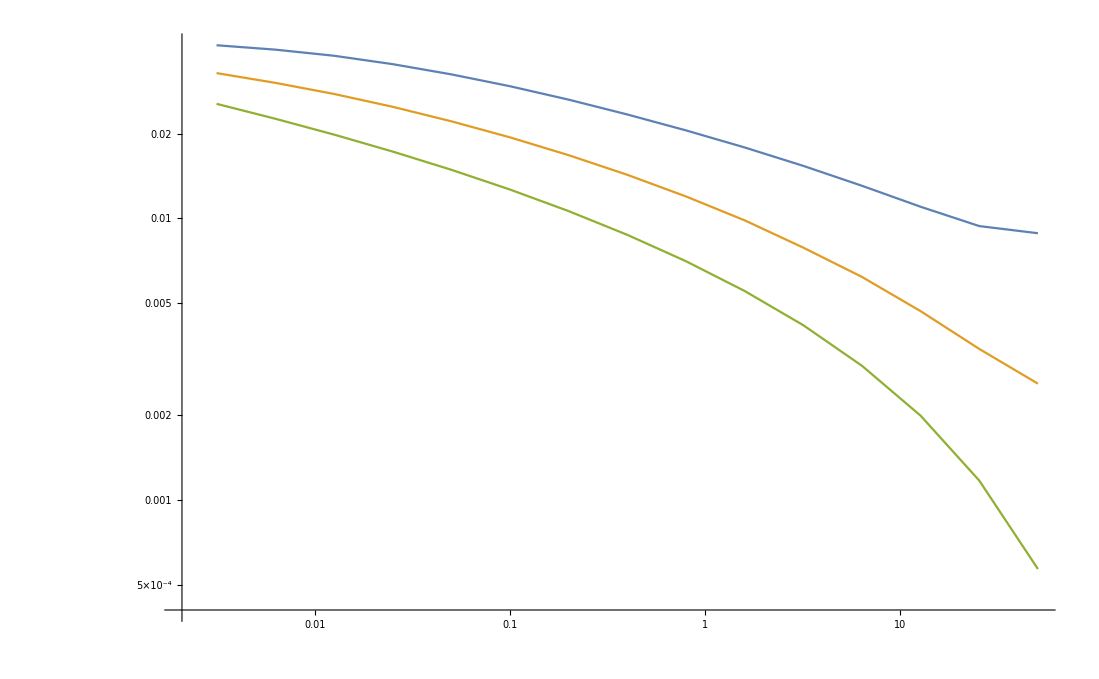

```mathematica
ListLogLogPlot[{mumu,mua,aa},Joined->True]
```

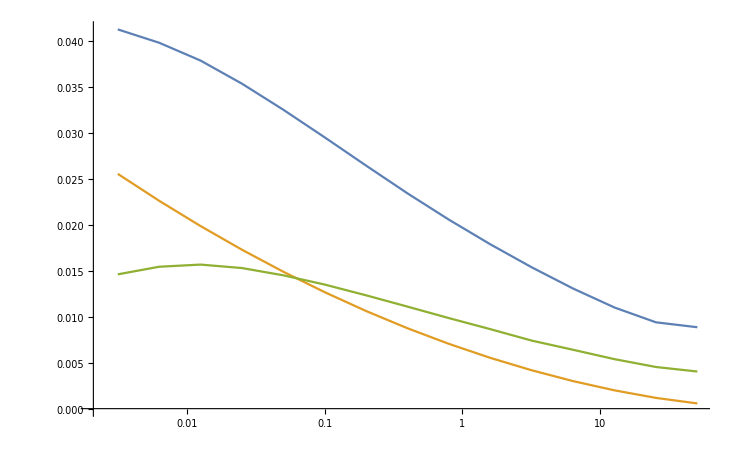

```mathematica
ListLogLinearPlot[{mumu,Dlog,Slog},Joined->True]
```

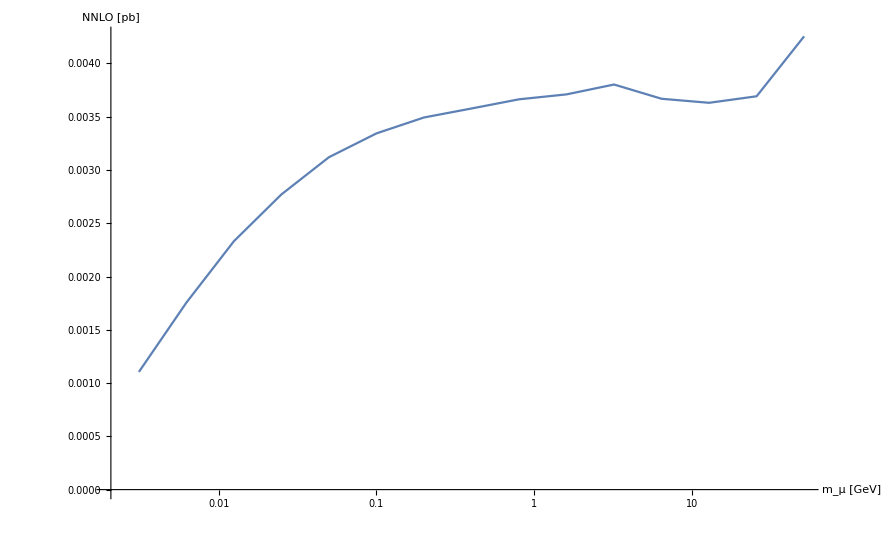

```mathematica
ListLogLinearPlot[diff[diff[mumu,Dlog],Slog],Joined->True,AxesLabel->{"m_μ [GeV]", "NNLO [pb]"}]
```

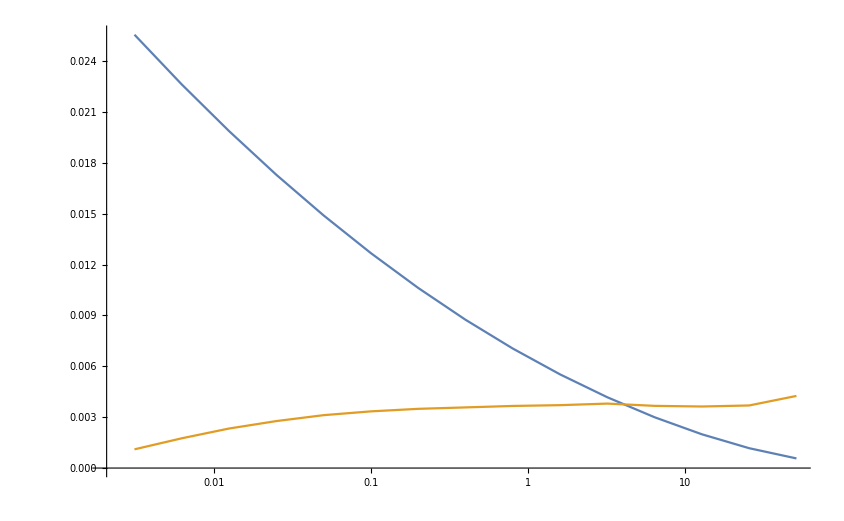

```mathematica
ListLogLinearPlot[{aa,diff[diff[mumu,Dlog],Slog]},Joined->True]
```

```mathematica
LO=Dlog
NLO=coeff[diff[mua,Dlog],2]
NNLO=diff[diff[mumu,Dlog],Slog]
```

{{0.003125,0.025565},{0.00625,0.02263},{0.0125,0.019879},{0.025,0.017301},{0.05,0.014903},{0.1,0.012678},{0.2,0.010626},{0.4,0.0087503},{0.8,0.0070516},{1.6,0.0055266},{3.2,0.0041763},{6.4,0.0029965},{12.8,0.0019915},{25.6,0.0011708},{51.2,0.00056764}}

{{0.003125,0.0146219},{0.00625,0.01545},{0.0125,0.0156847},{0.025,0.0153075},{0.05,0.0145161},{0.1,0.0135085},{0.2,0.012337},{0.4,0.0111063},{0.8,0.00985682},{1.6,0.00865416},{3.2,0.00740752},{6.4,0.00640783},{12.8,0.00538719},{25.6,0.00453579},{51.2,0.00404077}}

{{0.003125,0.00110466},{0.00625,0.00175572},{0.0125,0.002332},{0.025,0.00277132},{0.05,0.00312037},{0.1,0.00334395},{0.2,0.00349337},{0.4,0.0035777},{0.8,0.00366387},{1.6,0.00371015},{3.2,0.00380271},{6.4,0.00366892},{12.8,0.00363105},{25.6,0.00369233},{51.2,0.00425517}}

```mathematica
MyInterpol[x_]:=Interpolation[x,InterpolationOrder->1]
MyInterpolLog[x_]:=Interpolation[Map[{Log[#[[1]]],#[[2]]}&,x],InterpolationOrder->1]
```

```mathematica
(*METTI A POSTO*)
```

```mathematica
interpolLO= MyInterpol[LO]
interpolNLO= MyInterpol[NLO]
interpolNNLO= MyInterpol[NNLO]
interpolmumu= MyInterpol[mumu]

interpolLogLO= MyInterpolLog[LO]
interpolLogNLO= MyInterpolLog[NLO]
interpolLogNNLO= MyInterpolLog[NNLO]
interpolLogmumu= MyInterpolLog[mumu]

Which[energycollider===10,
interpolLOten= MyInterpol[LO];
interpolNLOten= MyInterpol[NLO];
interpolNNLOten= MyInterpol[NNLO];
interpolmumuten= MyInterpol[mumu];,
energycollider===1,
interpolLOone= MyInterpol[LO];
interpolNLOone= MyInterpol[NLO];
interpolNNLOone= MyInterpol[NNLO];
interpolmumuone= MyInterpol[mumu];,
energycollider===3,
interpolLOthree= MyInterpol[LO];
interpolNLOthree= MyInterpol[NLO];
interpolNNLOthree= MyInterpol[NNLO];
interpolmumuthree= MyInterpol[mumu];]

Which[energycollider===10,
interpolLogLOten= MyInterpolLog[LO];
interpolLogNLOten= MyInterpolLog[NLO];
interpolLogNNLOten= MyInterpolLog[NNLO];
interpolLogmumuten= MyInterpolLog[mumu];,
energycollider===1,
interpolLogLOone= MyInterpolLog[LO];
interpolLogNLOone= MyInterpolLog[NLO];
interpolLogNNLOone= MyInterpolLog[NNLO];
interpolLogmumuone= MyInterpolLog[mumu];,
energycollider===3,
interpolLogLOthree= MyInterpolLog[LO];
interpolLogNLOthree= MyInterpolLog[NLO];
interpolLogNNLOthree= MyInterpolLog[NNLO];
interpolLogmumuthree= MyInterpolLog[mumu];]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«5 more identical outputs»

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]

```mathematica
interpolLO[3]
interpolNLO[3]
interpolNNLO[3]
interpolmumu[3]
```

0.00434509

0.00756335

0.00379114

0.0156996

```mathematica
interpolLogLO[Log[3]]
interpolLogNLO[Log[3]]
interpolLogNNLO[Log[3]]
interpolLogmumu[Log[3]]
```

0.00430203

0.0075236

0.00379409

0.0156197

```mathematica
interpolLO[0.106]
interpolNLO[0.106]
interpolNNLO[0.106]
interpolmumu[0.106]
```

0.0125549

0.0134382

0.00335291

0.029346

```mathematica
interpolLogLO[Log[0.106]]
interpolLogNLO[Log[0.106]]
interpolLogNNLO[Log[0.106]]
interpolLogmumu[Log[0.106]]
```

0.0125055

0.01341

0.00335651

0.0292721

```mathematica
(*mmu=3 GeV,sqrts=10 TeV*)
 NLOMarco[3,10]= 0.008198769(*+-1.21944e-05*)
 LOMarco[3,10]= 0.004286358(*+-4.883389e-06*)
 NNLOMarco[3,10]= 0.003076577(*+-1.755674e-05*)
 TOTMarco[3,10]= 0.0155617(*+-3.207687e-05*)

(*sqrts=3 tev*)
 LOMarco[3,3]= 0.001167837(*+-9.464152e-07*)
 NLOMarco[3,3]= 0.002442781(*+-1.728379e-06*)
 NNLOMarco[3,3]= 0.0009963775(*+-8.595159e-07*)
 TOTMarco[3,3]= 0.004606996(*+-3.19933e-06*)

(*sqrts=1tev*)
 LOMarco[3,1]= 0.0001274048(*+-6.556385e-08*)
 NLOMarco[3,1]= 0.000239246(*+-5.560011e-08*)
 NNLOMarco[3,1]= 7.990717/100000(*+-5.069922e-08*)
 TOTMarco[3,1]= 0.0004465579(*+-8.302236e-08*)


(*mmu=0.106…, sqrts=10 TeV*)
 LOMarco[0.106,10]= 0.01248962(*+-1.225966e-05*)
 NLOMarco[0.106,10]= 0.01385342(*+-8.933496e-06*)
 NNLOMarco[0.106,10]= 0.003090965(*+-3.210552e-05*)
 TOTMarco[0.106,10]= 0.02943401(*+-2.931572e-05*)

(*sqrts=3 tev*)
 LOMarco[0.106,3]= 0.00410878(*+-2.65797e-06*)
 NLOMarco[0.106,3]= 0.004594361(*+-3.445651e-06*)
 NNLOMarco[0.106,3]= 0.0010012(*+-2.408735e-06*)
 TOTMarco[0.106,3]= 0.009704341(*+-3.401229e-06*)
(*sqrts=1 tev*)
 LOMarco[0.106,1]= 0.000563051(*+-1.64222e-07*)
 NLOMarco[0.106,1]= 0.0005104588(*+-2.398158e-07*)
 NNLOMarco[0.106,1] =8.004164/100000(*+-8.70176e-08*)
 TOTMarco[0.106,1]= 0.001153551(*+-1.380072e-07*)



(*mmu=3.2 GeV,sqrts=10 TeV*)
 NLOMarco[3.2,10]= 0.008090235(*+-1.202481e-05*)
 LOMarco[3.2,10]= 0.004168312(*+-4.706369e-06*)
 NNLOMarco[3.2,10]= 0.003076552(*+-1.752871e-05*)
 TOTMarco[3.2,10]= 0.0153351(*+-3.173795e-05*)
```

0.00819877

0.00428636

0.00307658

0.0155617

0.00116784

0.00244278

0.000996378

0.004607

0.000127405

0.000239246

0.0000799072

0.000446558

0.0124896

0.0138534

0.00309097

0.029434

0.00410878

0.00459436

0.0010012

0.00970434

0.000563051

0.000510459

0.0000800416

0.00115355

0.00809024

0.00416831

0.00307655

0.0153351

```mathematica
NNLO
```

{{0.003125,0.00110466},{0.00625,0.00175572},{0.0125,0.002332},{0.025,0.00277132},{0.05,0.00312037},{0.1,0.00334395},{0.2,0.00349337},{0.4,0.0035777},{0.8,0.00366387},{1.6,0.00371015},{3.2,0.00380271},{6.4,0.00366892},{12.8,0.00363105},{25.6,0.00369233},{51.2,0.00425517}}

```mathematica
interpolNNLOten[3.2]
```

0.00380271

PUNTIESATTI

```mathematica
(*mmu=3.2, sqrts=10 TeV*)
checkLO={LOMarco[3.2,10]/interpolLOten[3.2],(LOMarco[3.2,10]-interpolLOten[3.2])/LOMarco[3.2,10]}
checkNLO= {NLOMarco[3.2,10]/interpolNLOten[3.2],(NLOMarco[3.2,10]-interpolNLOten[3.2])/LOMarco[3.2,10]}
 checkNNLO={NNLOMarco[3.2,10]/interpolNNLOten[3.2],(NNLOMarco[3.2,10]-interpolNNLOten[3.2])/LOMarco[3.2,10]}
 checkTOTLO={TOTMarco[3.2,10]/interpolmumuten[3.2],(TOTMarco[3.2,10]-interpolmumuten[3.2])/LOMarco[3.2,10]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.998087,-0.00191636}

{1.09216,0.163786}

{0.809042,-0.174209}

{0.996657,-0.0123391}

-0.0123393

INTERPOLAZIONE LINEARE

```mathematica
(*mmu=0.106…,sqrts=10 tev*)
 checkLO={LOMarco[0.106,10]/interpolLOten[0.106],(LOMarco[0.106,10]-interpolLOten[0.106])/LOMarco[0.106,10]}
checkNLO= {NLOMarco[0.106,10]/interpolNLOten[0.106],(NLOMarco[0.106,10]-interpolNLOten[0.106])/LOMarco[0.106,10]}
 checkNNLO={NNLOMarco[0.106,10]/interpolNNLOten[0.106],(NNLOMarco[0.106,10]-interpolNNLOten[0.106])/LOMarco[0.106,10]}
 checkTOTLO={TOTMarco[0.106,10]/interpolmumuten[0.106],(TOTMarco[0.106,10]-interpolmumuten[0.106])/LOMarco[0.106,10]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.994802,-0.00522514}

{1.0309,0.0332424}

{0.921875,-0.0209731}

{1.003,0.00704456}

0.00704416

```mathematica
(*mmu=0.106…,sqrts=3 tev*)
 checkLO={LOMarco[0.106,3]/interpolLOthree[0.106],(LOMarco[0.106,3]-interpolLOthree[0.106])/LOMarco[0.106,3]}
checkNLO= {NLOMarco[0.106,3]/interpolNLOthree[0.106],(NLOMarco[0.106,3]-interpolNLOthree[0.106])/LOMarco[0.106,3]}
 checkNNLO={NNLOMarco[0.106,3]/interpolNNLOthree[0.106],(NNLOMarco[0.106,3]-interpolNNLOthree[0.106])/LOMarco[0.106,3]}
 checkTOTLO={TOTMarco[0.106,3]/interpolmumuthree[0.106],(TOTMarco[0.106,3]-interpolmumuthree[0.106])/LOMarco[0.106,3]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.995087,-0.00493723}

{1.0076,0.00843679}

{0.954362,-0.0116525}

{0.99656,-0.00815297}

-0.00815297

```mathematica
(*mmu=0.106…,sqrts=1 tev*)
 checkLO={LOMarco[0.106,1]/interpolLOone[0.106],(LOMarco[0.106,1]-interpolLOone[0.106])/LOMarco[0.106,1]}
checkNLO= {NLOMarco[0.106,1]/interpolNLOone[0.106],(NLOMarco[0.106,1]-interpolNLOone[0.106])/LOMarco[0.106,1]}
 checkNNLO={NNLOMarco[0.106,1]/interpolNNLOone[0.106],(NNLOMarco[0.106,1]-interpolNNLOone[0.106])/LOMarco[0.106,1]}
 checkTOTLO={TOTMarco[0.106,1]/interpolmumuone[0.106],(TOTMarco[0.106,1]-interpolmumuone[0.106])/LOMarco[0.106,1]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.995449,-0.00457223}

{0.999385,-0.000557844}

{0.990437,-0.00137253}

{0.996836,-0.00650339}

-0.00650261

```mathematica
(*mmu=3, sqrts=10 TeV*)
checkLO={LOMarco[3,10]/interpolLOten[3],(LOMarco[3,10]-interpolLOten[3])/LOMarco[3,10]}
checkNLO= {NLOMarco[3,10]/interpolNLOten[3],(NLOMarco[3,10]-interpolNLOten[3])/LOMarco[3,10]}
 checkNNLO={NNLOMarco[3,10]/interpolNNLOten[3],(NNLOMarco[3,10]-interpolNNLOten[3])/LOMarco[3,10]}
 checkTOTLO={TOTMarco[3,10]/interpolmumuten[3],(TOTMarco[3,10]-interpolmumuten[3])/LOMarco[3,10]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.986484,-0.0137015}

{1.08401,0.148241}

{0.811518,-0.166706}

{0.991218,-0.0321672}

-0.0321663

```mathematica
(*mmu=3,sqrts=3 tev*)
 checkLO={LOMarco[3,3]/interpolLOthree[3],(LOMarco[3,3]-interpolLOthree[3])/LOMarco[3,3]}
checkNLO= {NLOMarco[3,3]/interpolNLOthree[3],(NLOMarco[3,3]-interpolNLOthree[3])/LOMarco[3,3]}
 checkNNLO={NNLOMarco[3,3]/interpolNNLOthree[3],(NNLOMarco[3,3]-interpolNNLOthree[3])/LOMarco[3,3]}
 checkTOTLO={TOTMarco[3,3]/interpolmumuthree[3],(TOTMarco[3,3]-interpolmumuthree[3])/LOMarco[3,3]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.983752,-0.016516}

{1.0246,0.050215}

{0.924748,-0.0694281}

{0.991024,-0.0357287}

-0.0357291

```mathematica
(*mmu=3, sqrts=1 TeV*)
  checkLO={LOMarco[3,1]/interpolLOone[3],(LOMarco[3,1]-interpolLOone[3])/LOMarco[3,1]}
checkNLO= {NLOMarco[3,1]/interpolNLOone[3],(NLOMarco[3,1]-interpolNLOone[3])/LOMarco[3,1]}
 checkNNLO={NNLOMarco[3,1]/interpolNNLOone[3],(NNLOMarco[3,1]-interpolNNLOone[3])/LOMarco[3,1]}
 checkTOTLO={TOTMarco[3,1]/interpolmumuone[3],(TOTMarco[3,1]-interpolmumuone[3])/LOMarco[3,1]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.980376,-0.0200165}

{0.99424,-0.0108788}

{0.983149,-0.0107501}

{0.988258,-0.0416461}

-0.0416455

INTERPOLAZIONE Logaritmica

```mathematica
(*mmu=0.106…,sqrts=10 tev*)
 checkLO={LOMarco[0.106,10]/interpolLogLOten[Log[0.106]],(LOMarco[0.106,10]-interpolLogLOten[Log[0.106]])/LOMarco[0.106,10]}
checkNLO= {NLOMarco[0.106,10]/interpolLogNLOten[Log[0.106]],(NLOMarco[0.106,10]-interpolLogNLOten[Log[0.106]])/LOMarco[0.106,10]}
 checkNNLO={NNLOMarco[0.106,10]/interpolLogNNLOten[Log[0.106]],(NNLOMarco[0.106,10]-interpolLogNNLOten[Log[0.106]])/LOMarco[0.106,10]}
 checkTOTLO={TOTMarco[0.106,10]/interpolLogmumuten[Log[0.106]],(TOTMarco[0.106,10]-interpolLogmumuten[Log[0.106]])/LOMarco[0.106,10]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.99873,-0.00127147}

{1.03306,0.0354996}

{0.920887,-0.021261}

{1.00553,0.0129675}

0.0129671

```mathematica
(*mmu=0.106…,sqrts=3 tev*)
 checkLO={LOMarco[0.106,3]/interpolLogLOthree[Log[0.106]],(LOMarco[0.106,3]-interpolLogLOthree[Log[0.106]])/LOMarco[0.106,3]}
checkNLO= {NLOMarco[0.106,3]/interpolLogNLOthree[Log[0.106]],(NLOMarco[0.106,3]-interpolLogNLOthree[Log[0.106]])/LOMarco[0.106,3]}
 checkNNLO={NNLOMarco[0.106,3]/interpolLogNNLOthree[Log[0.106]],(NNLOMarco[0.106,3]-interpolLogNNLOthree[Log[0.106]])/LOMarco[0.106,3]}
 checkTOTLO={TOTMarco[0.106,3]/interpolLogmumuthree[Log[0.106]],(TOTMarco[0.106,3]-interpolLogmumuthree[Log[0.106]])/LOMarco[0.106,3]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.999508,-0.000492513}

{1.01001,0.0110767}

{0.954376,-0.0116488}

{0.999549,-0.00106462}

-0.00106462

```mathematica
(*mmu=0.106…,sqrts=1 tev*)
 checkLO={LOMarco[0.106,1]/interpolLogLOone[Log[0.106]],(LOMarco[0.106,1]-interpolLogLOone[Log[0.106]])/LOMarco[0.106,1]}
checkNLO= {NLOMarco[0.106,1]/interpolLogNLOone[Log[0.106]],(NLOMarco[0.106,1]-interpolLogNLOone[Log[0.106]])/LOMarco[0.106,1]}
 checkNNLO={NNLOMarco[0.106,1]/interpolLogNNLOone[Log[0.106]],(NNLOMarco[0.106,1]-interpolLogNNLOone[Log[0.106]])/LOMarco[0.106,1]}
 checkTOTLO={TOTMarco[0.106,1]/interpolLogmumuone[Log[0.106]],(TOTMarco[0.106,1]-interpolLogmumuone[Log[0.106]])/LOMarco[0.106,1]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{1.0004,0.00040302}

{1.00205,0.00185863}

{0.990352,-0.00138485}

{1.00043,0.000876022}

0.000876804

```mathematica
(*mmu=3, sqrts=10 TeV*)
checkLO={LOMarco[3,10]/interpolLogLOten[Log[3]],(LOMarco[3,10]-interpolLogLOten[Log[3]])/LOMarco[3,10]}
checkNLO= {NLOMarco[3,10]/interpolLogNLOten[Log[3]],(NLOMarco[3,10]-interpolLogNLOten[Log[3]])/LOMarco[3,10]}
 checkNNLO={NNLOMarco[3,10]/interpolLogNNLOten[Log[3]],(NNLOMarco[3,10]-interpolLogNNLOten[Log[3]])/LOMarco[3,10]}
 checkTOTLO={TOTMarco[3,10]/interpolLogmumuten[Log[3]],(TOTMarco[3,10]-interpolLogmumuten[Log[3]])/LOMarco[3,10]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.996358,-0.00365523}

{1.08974,0.157516}

{0.810886,-0.167395}

{0.996286,-0.0135346}

-0.0135337

```mathematica
(*mmu=3,sqrts=3 tev*)
 checkLO={LOMarco[3,3]/interpolLogLOthree[Log[3]],(LOMarco[3,3]-interpolLogLOthree[Log[3]])/LOMarco[3,3]}
checkNLO= {NLOMarco[3,3]/interpolLogNLOthree[Log[3]],(NLOMarco[3,3]-interpolLogNLOthree[Log[3]])/LOMarco[3,3]}
 checkNNLO={NNLOMarco[3,3]/interpolLogNNLOthree[Log[3]],(NNLOMarco[3,3]-interpolLogNNLOthree[Log[3]])/LOMarco[3,3]}
 checkTOTLO={TOTMarco[3,3]/interpolLogmumuthree[Log[3]],(TOTMarco[3,3]-interpolLogmumuthree[Log[3]])/LOMarco[3,3]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.996023,-0.00399283}

{1.03057,0.0620561}

{0.925103,-0.0690744}

{0.997217,-0.0110107}

-0.0110111

```mathematica
(*mmu=3, sqrts=1 TeV*)
  checkLO={LOMarco[3,1]/interpolLogLOone[Log[3]],(LOMarco[3,1]-interpolLogLOone[Log[3]])/LOMarco[3,1]}
checkNLO= {NLOMarco[3,1]/interpolLogNLOone[Log[3]],(NLOMarco[3,1]-interpolLogNLOone[Log[3]])/LOMarco[3,1]}
 checkNNLO={NNLOMarco[3,1]/interpolLogNNLOone[Log[3]],(NNLOMarco[3,1]-interpolLogNNLOone[Log[3]])/LOMarco[3,1]}
 checkTOTLO={TOTMarco[3,1]/interpolLogmumuone[Log[3]],(TOTMarco[3,1]-interpolLogmumuone[Log[3]])/LOMarco[3,1]}

checkLO[[2]]+checkNLO[[2]]+checkNNLO[[2]]
```

{0.99597,-0.00404679}

{1.00164,0.00306707}

{0.98307,-0.0108012}

{0.99665,-0.0117815}

-0.0117809

```mathematica
interpolLOone[3]+interpolNLOone[3]+interpolNNLOone[3]
interpolmumuone[3]
```

0.000451864

0.000451864

```mathematica
interpolLOten[0.106]
interpolLOnew= Interpolation[LO,InterpolationOrder->1]
interpolLOnew[0.106]
```

0.0125549

InterpolatingFunction[…]

0.0125549

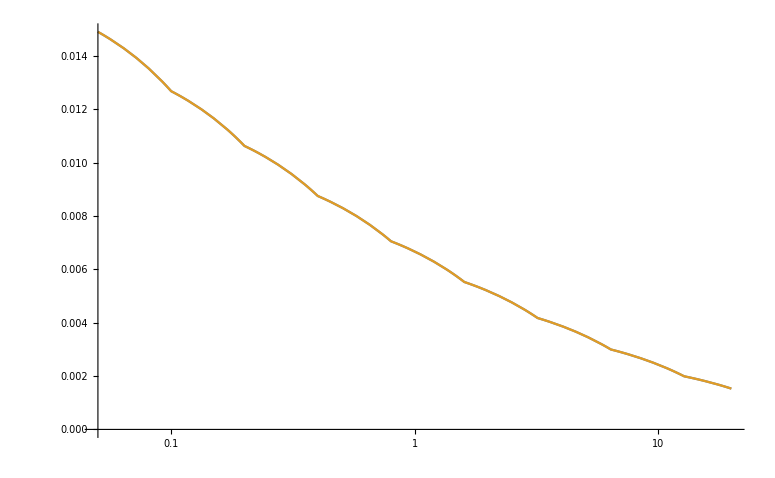

```mathematica
LogLinearPlot[{interpolLOten[x],interpolLOnew[x]},{x,0.05,20}]
```

```mathematica
LO
```

{{0.003125,0.025565},{0.00625,0.02263},{0.0125,0.019879},{0.025,0.017301},{0.05,0.014903},{0.1,0.012678},{0.2,0.010626},{0.4,0.0087503},{0.8,0.0070516},{1.6,0.0055266},{3.2,0.0041763},{6.4,0.0029965},{12.8,0.0019915},{25.6,0.0011708},{51.2,0.00056764}}

```mathematica
interpolLOten[0.1]
interpolLOten[0.106]
```

0.012678

0.0125549

```mathematica
0.012678
```

0.012678

```mathematica
interpolLOten[3]
interpolLOten[3.2]
```

0.00434509

0.0041763

```mathematica
1/0.0072992701
```

137.

```mathematica
LOMarco[0.106,3]
NLOMarco[0.106,3]
NNLOMarco[0.106,3]
```

0.00410878

0.00459436

0.0010012